# Mathematica HW 1: June 19, 2022

Plot and analyze the solutions of a simple second order differential equation.

```mathematica
solution = DSolve[{y''[x]+(w^2)y[x]==0,y[0]==1,y'[0]==0},y[x],x]
(*DSolve[{y''[x]+(w^2)y[x]==0,y[0]==1},y[x],x]*)
```

{{y[x]→Cos[w x]}}

```mathematica
f[x_]=y[x]/.solution[[1]]
```

Cos[w x]

Cos[x]

{-Sin[x]}

InterpolatingFunction[…][x]

{InterpolatingFunction[…][x]}

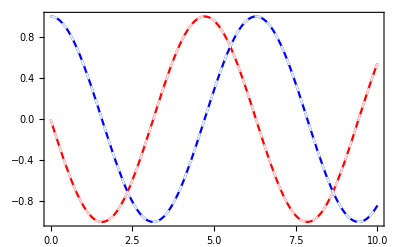

```mathematica
w:=1
solution := DSolve[{y''[x]+(w^2)y[x]==0,y[0]==1,y'[0]==0},y[x],x]
nsolution := NDSolve[{y''[x]+(w^2)y[x]==0,y[0]==1,y'[0]==0},y[x],{x,0,10}]
f[x_]=y[x]/.solution[[1]] 
df[x_]=D[f[x],x]/.solution
(*F[x_]=Integrate[f[x],x]*)
nf[x_]=y[x]/.nsolution[[1]]
ndf[x_]=D[nf[x],x]/.nsolution
(*nF=Integrate[nf,x]*)
Show[{
Plot[{f[x]},{x,0, 10}, Frame -> True, PlotStyle->{Blue}],
Plot[{df[x]},{x,0, 10}, Frame -> True, PlotStyle->{Red}],
Plot[{nf[x]},{x,0,10}, Frame -> True, PlotStyle->{LightBlue, Dashed}],
Plot[{ndf[x]},{x,0,10}, Frame -> True, PlotStyle->{LightRed, Dashed}]
}]
```